# Physics through Computational Thinking Week-4: Solving Initial Value Problems

In this tutorial, we explore the mathematical and computational tools needed to model physical systems using differential equations. We will discuss initial value problems and introduce Euler’s method as a first step toward numerical solutions of differential equations.

## 1. Essential Calculus Tools

```mathematica
Clear[x];
```

```mathematica
f[x_]:=x^3 Exp[-x];
```

```mathematica
D[f[x],x]
```

3 ⅇ^-x x^2-ⅇ^-x x^3

```mathematica
D[f[x],{x,3}]
```

6 ⅇ^-x-18 ⅇ^-x x+9 ⅇ^-x x^2-ⅇ^-x x^3

Ex.-1: Compute the third derivative of  g(x)=Sin(x^2) .

```mathematica
Clear[x,g];
```

```mathematica
g[x_]:=Sin[x^2];
```

```mathematica
D[g[x],{x,3}]
```

-8 x^3 Cos[x^2]-12 x Sin[x^2]

```mathematica
Integrate[x Exp[-x],x]
```

ⅇ^-x (-1-x)

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
```

π/2

```mathematica
Series[Exp[x],{x,0,5}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O[x]^6

Take the previous output (%) and convert it to its normal (ordinary) form.

```mathematica
Normal[%]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120

It removes the O[x]^6 term.

Manipulating Lists in Mathematica

```mathematica
list=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
f[x_]:=x^2;
```

```mathematica
f/@list
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
list
```

{1,2,3,4,5,6,7,8,9,10}

Here /@ -> mapping

```mathematica
Map[f,list]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Sin@(Pi/4)
```

1/(√2)

Here @ -> prefix form

```mathematica
Sin@Pi
```

0

```mathematica
Plus@@list
```

55

Here @@ -> apply

```mathematica
list1={1,2}
```

{1,2}

```mathematica
Times@@list1
```

2

```mathematica
Plus@@list1
```

3

```mathematica
data=RandomReal[1,20]
```

{0.879224,0.45815,0.744838,0.96392,0.851232,0.813789,0.868137,0.418396,0.197809,0.58018,0.964096,0.502945,0.531959,0.591376,0.607631,0.501962,0.477524,0.55362,0.619428,0.952414}

```mathematica
Select[data,#>0.8&]
```

{0.879224,0.96392,0.851232,0.813789,0.868137,0.964096,0.952414}

Ex.-2: make a list from the data where Sqrt[data]>0.5 .

```mathematica
Select[data,Sqrt[#]>0.9&]
```

{0.879224,0.96392,0.851232,0.813789,0.868137,0.964096,0.952414}

## 2. Initial Value Problems

Let’s consider

(d y)/dt=-2 y ,  with  y(0)=1.      -- (1)

```mathematica
sol=DSolve[{y'[t]==-2 y[t],y[0]==1},y[t],t] (*analytic solutions*)
```

{{y[t]→ⅇ^(-2 t)}}

Numerical Solutions

```mathematica
nsol=NDSolve[{y'[t]==-2 y[t],y[0]==1},y,{t,0,5}]
```

{{y→InterpolatingFunction[…]}}

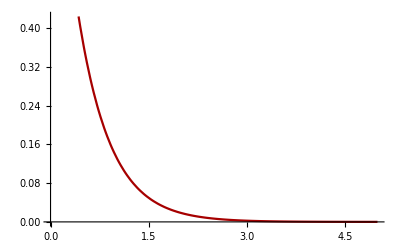

```mathematica
Plot[Evaluate[y[t]/. nsol],{t,0,5}]
```

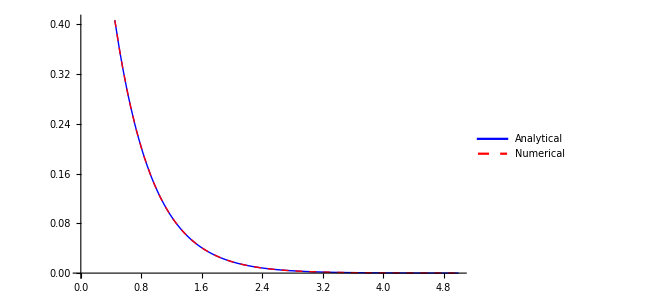

```mathematica
Plot[{Evaluate[y[t]/. sol[[1]]],Evaluate[y[t]/. nsol]},{t,0,5},PlotLegends->{"Analytical","Numerical"},PlotStyle->{Directive[Blue,Thick],Directive[Red,Dashed,Thick]}]
```

Euler’s Method

Now, we solve equation (1) using Euler’s method.

y_(n+1)=y_n+h f(t_n,y_n)
t_(n+1)=t_n+h

Let’s implement this in Mathematica.

```mathematica
Clear[f,h,t0,y0,n];
```

```mathematica
f[t_,y_]:=-2 y;
```

```mathematica
h=0.1;
t0=0;
y0=1;
n=50;
```

```mathematica
euler=NestList[{#[[1]]+h,#[[2]]+h f[#[[1]],#[[2]]]}&,{t0,y0},n];
```

Start from (t_o,y_0), apply y_n+h f(t_n,y_n) repeatedly n times, and store all intermediate results.

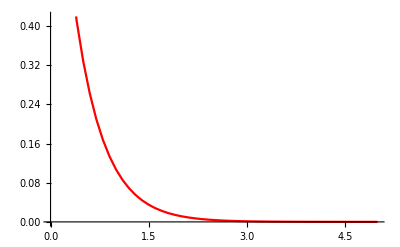

```mathematica
ListLinePlot[euler,PlotStyle->Red]
```

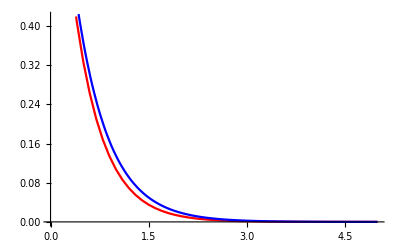

```mathematica
Show[ListLinePlot[euler,PlotStyle->Red],Plot[Exp[-2 t],{t,0,5},PlotStyle->Blue]]
```

Ex.-3: change the step size h=0.5 and observe the difference.

```mathematica
h=0.5
```

0.5

```mathematica
euler=NestList[{#[[1]]+h,#[[2]]+h f[#[[1]],#[[2]]]}&,{t0,y0},n];
```

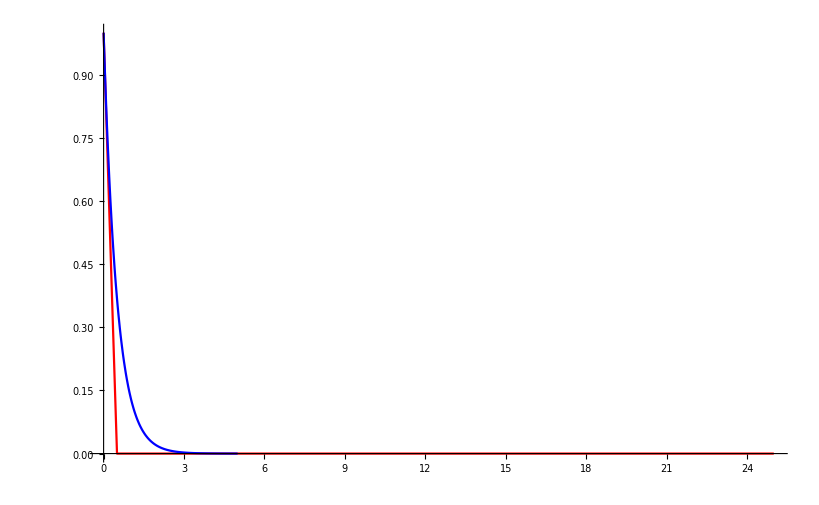

```mathematica
Show[ListLinePlot[euler,PlotStyle->Red,PlotRange->All],Plot[Exp[-2 t],{t,0,5},PlotStyle->Blue,PlotRange->All]]
```

```mathematica
h=0.05
```

0.05

```mathematica
euler=NestList[{#[[1]]+h,#[[2]]+h f[#[[1]],#[[2]]]}&,{t0,y0},n];
```

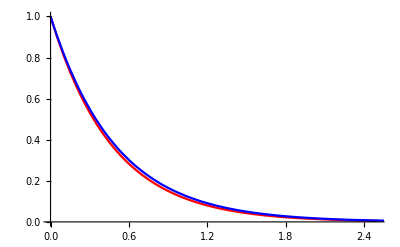

```mathematica
Show[ListLinePlot[euler,PlotStyle->Red,PlotRange->All],Plot[Exp[-2 t],{t,0,5},PlotStyle->Blue,PlotRange->All]]
```

Euler is a first-order approximation. If step size is too large:
  (i) It overshoots the slope, (ii) It accumulates large truncation errors (see above), (iii) It amplifies error instead of damping it.

Euler’s method is conditionally stable.

```mathematica
EulerMethod[h_,n_]:=Module[{t=0,y=1,data={{0,1}}},Do[y=y+h f[t,y];
t=t+h;
AppendTo[data,{t,y}],{n}];
data]
```

```mathematica
Manipulate[Show[{Plot[Exp[-2 t],{t,0,5},PlotStyle->{Black,Thick}],ListLinePlot[EulerMethod[h,Round[5/h]],PlotStyle->{Red}]},PlotRange->{{0,5},{-2,2}}],{h,0.05,1.5}]
```

```mathematica
EulerMethod[h_]:=Module[{t=0,y=1},While[t<5,y=y+h (-2 y);
t=t+h;];
y]
```

```mathematica
Table[{h,EulerMethod[h],N[Exp[-10]],Abs[EulerMethod[h]-Exp[-10]]},{h,{0.2,0.1,0.05,0.01}}]
```

{{0.2,2.84303×10^-6,0.0000453999,0.0000425569},{0.1,0.0000142725,0.0000453999,0.0000311275},{0.05,0.0000265614,0.0000453999,0.0000188385},{0.01,0.000041024,0.0000453999,4.37594×10^-6}}

Does reducing h reduce error?

Euler’s method has:
Local truncation error ≈ O(h^2)
Global error ≈ O(h)  -- it’s large

=> Local truncation error accumulates into global error.

Damped Harmonic Oscillator

Let’s consider the equation

m d^2/dt^2 y(t) + γ d/dt y(t) + k x(t)=0

```mathematica
m=1;
γ=0.5;
k=4;
```

```mathematica
sol=DSolve[{m x''[t]+γ x'[t]+k x[t]==0,x[0]==1,x'[0]==0},x[t],t]
```

{{x[t]→1. ⅇ^(-0.25 t) (1. Cos[1.98431 t]+0.125988 Sin[1.98431 t])}}

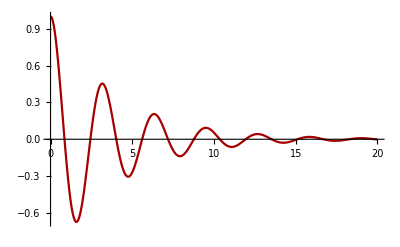

```mathematica
Plot[Evaluate[x[t]/. sol[[1]]],{t,0,20},PlotRange->All]
```

Ex. -4: Change γ=5 and compare behaviors.

LCR Circuit Analogy

L  d^2/dt^2 q(t) + R d/dt q(t) + 1/C_0 q(t)=0

```mathematica
Clear[L,R,C0]
```

```mathematica
L=1;
R=0.5;
C0=0.25;
```

```mathematica
solLCR=DSolve[{L q''[t]+R q'[t]+(1/C0) q[t]==0,q[0]==1,q'[0]==0},q[t],t]
```

{{q[t]→1. ⅇ^(-0.25 t) (1. Cos[1.98431 t]+0.125988 Sin[1.98431 t])}}

```mathematica
Plot[Evaluate[q[t]/. solLCR[[1]]],{t,0,20},PlotRange->All]
```

-Graphics-

Ex.-5: Study forced oscillator:

L  d^2/dt^2 q(t) + R d/dt q(t) + 1/C_0 q(t)=F cos(ω t)

Example

For mass-spring system, the equation derived from Newton’s second law:

F=m (d^2 x)/dt^2=-k x

This can be written as a set of coupled equations:

m (d v)/dt=-k x ,
v=(d x)/dt,

where v is the velocity. We solved iteratively

v_(n+1)=v_(n-1)-(2h k)/m x_n ,
x_(n+1)=x_(n-1)+ 2h v_n .

We discuss this with different initial conditions and h values to explore the behavior of the algorithm.

```mathematica
Quit[];
```

```mathematica
Clear[x0,v0,t0,m,k];
```

```mathematica
x0 = 10.0;
v0 = -11.2;
t0 = 0.0;
m = 0.33;
k = 300.0;
```

```mathematica
step = 0.01;
t1 = t0 + step;
x1 = x0 + v0*step;
v1 = v0 - ( step*k*x0/m);
```

```mathematica
tmin = 2*step;
tmax = 1.0;
```

```mathematica
xin = x0;   
vin= v0;  
xmid     = x1; 
vmid     = v1;
```

```mathematica
velTab=Table[
	{t, 		
		vp = vin - (2*step*k/m)*xmid;
		xp =  xin + (2*step*vmid);			
		vin = vmid;
		vmid = vp;
		xin = xmid;
		xmid = xp
	},
	{t,tmin,tmax,step}
];
```

```mathematica
velTab = Prepend[velTab,{t1,v1}];
velTab = Prepend[velTab,{t0,v0}];
```

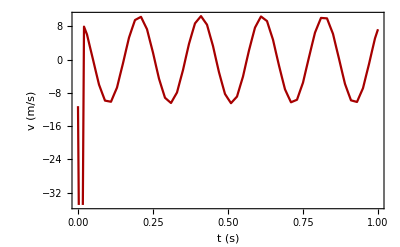

```mathematica
ListPlot[velTab,PlotRange->Automatic,Joined->True,Frame->True,FrameLabel->{"t (s)","v (m/s)"}]
```

```mathematica
xin = x0;   
vin= v0;   
xmid     = x1;   
vmid     = v1;
```

```mathematica
posTab = Table[
	{t, 		
		vp = vin - (2*step*k/m)*xmid;
		xp =  xin + (2*step*vmid);			
		vin = vmid;
		vmid = vp;
		xin = xmid;
		xmid = xp
	},
	{t,tmin,tmax,step}
];
```

```mathematica
posTab = Prepend[posTab,{t1,x1}];
posTab = Prepend[posTab,{t0,x0}];
```

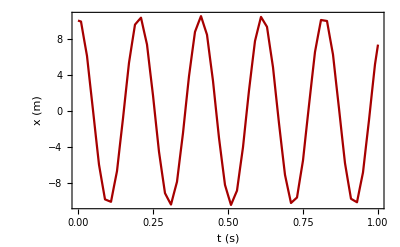

```mathematica
ListPlot[posTab,PlotRange->Automatic,Joined->True,Frame->True,FrameLabel->{"t (s)","x (m)"}]
```

Problem-1: Consider the initial value problem given by d/dt x=2t+4 x
and 𝑥(0)=1. If we numerically solve this problem using Euler’s method with x_0=x(0)=1 and h=0.2 , then the value of x_4 is

```mathematica
Clear[f,h]

f[t_,x_]:=2t+4 x;
h=0.2;

euler=NestList[{#[[1]]+h,#[[2]]+h f[#[[1]],#[[2]]]}&,{0,1},4];
```

```mathematica
euler
```

{{0,1},{0.2,1.8},{0.4,3.32},{0.6,6.136},{0.8,11.2848}}

Thus, x_4=11.2848 (ans).

Problem-2: Consider following initial value problem: d/dt x(t)=-2x t , with x(0)=2.

Plot x(t) vs. t .

```mathematica
sol=DSolve[{x'[t]+2 x[t]t==0,x[0]==2},x[t],t]
```

{{x[t]→2 ⅇ^(-t^2)}}

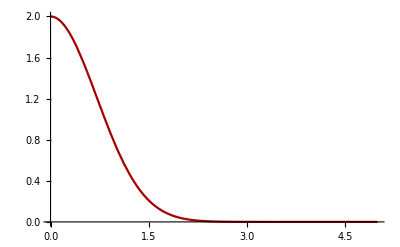

```mathematica
Plot[Evaluate[x[t]/. sol[[1]]],{t,0,5}]
```

## 3. Curve Fitting and Parameter Estimation

We want to extract physical constants (e.g., G or k) from noisy experimental data.

Linear Fit

```mathematica
ClearAll[x]
data=Table[{x,2 x+1+RandomVariate[NormalDistribution[0,0.5]]},{x,0,10,1}];
```

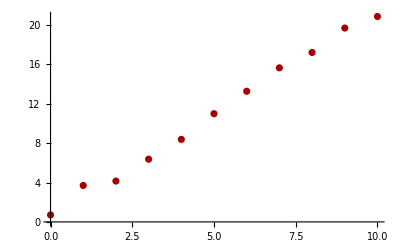

```mathematica
ListPlot[data]
```

To fit a model of the form a x+b 1 :

```mathematica
Lm=LinearModelFit[data,{x,1},x];
Lm["BestFitParameters"] (* best fit value of {a,b} *)
```

{2.06822,0.66293}

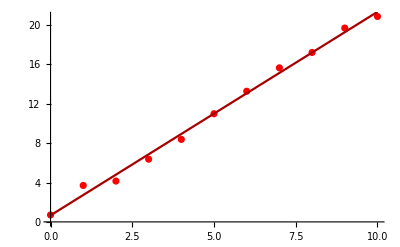

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[Lm[x],{x,Min[data[[All,1]]],Max[data[[All,1]]]}]]
```

Parameter Errors and Covariance Matrix:

```mathematica
Lm["ParameterErrors"]
Lm["CovarianceMatrix"]
```

{0.0514938,0.304642}

{{0.00265161,-0.0132581},{-0.0132581,0.0928065}}

```mathematica
{0.0514938240411878,0.30464157136456}^2
```

{0.00265161,0.0928065}

Ex-1: Let’s generate pseudo data that mimics a real experiment, such as a falling object (v=v_0+g t).

```mathematica
v0=2.5;
g=9.8;
data=Table[{t,v0+g*t+RandomReal[{-1,1}]},{t,0,5,0.5}];
```

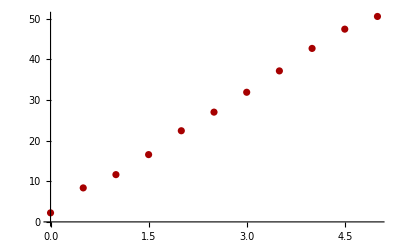

```mathematica
ListPlot[data]
```

```mathematica
Lm=LinearModelFit[data,{1,t},t]; (* Perform the fit *)
Lm["BestFitParameters"] (* Returns {v0,g}*)
Lm["ParameterTable"]
```

{2.45976,9.84282}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.45976 | 0.399189 | 6.16188 | 0.00016632
t | 9.84282 | 0.134951 | 72.9365 | 8.65693×10^-14

```mathematica
Lm["ParameterErrors"]
```

{0.399189,0.134951}

Note: (i)  t==(Estimated Value)/(Standard Error) (signal-to-noise ratio) , high t-statistic suggest that the effect is real.

(ii) p-value -- represents the probability that you would see your result if the true parameter value was actually zero (the "null hypothesis"). A small p-value means your parameter is “statistically significant”.

Most physics models (e.g., radioactive decay) are nonlinear.

```mathematica
NLm=NonlinearModelFit[data,a*x+b,{a,b},x];
NLm["BestFitParameters"]
```

{a→9.84282,b→2.45976}

Ex-2: Radioactive Decay, N(t)=N_0 e^(-λ t) :

```mathematica
decayData=Table[{t,100*Exp[-0.5*t]+RandomReal[{-2,2}]},{t,0,10,1}];
```

```mathematica
NLm=NonlinearModelFit[decayData,n0*Exp[-lambda*t],{n0,lambda},t]; (*Fit the model*)
```

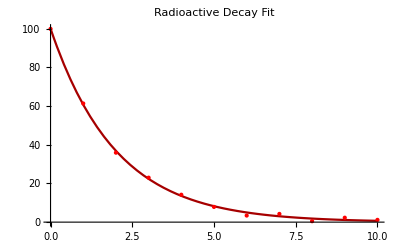

```mathematica
Plot[NLm[t],{t,0,10},Epilog->{Red,PointSize[Medium],Point[decayData]},PlotLabel->"Radioactive Decay Fit"]  (*Visualize the fit*)
```

```mathematica
NLm["BestFitParameters"]
```

{n0→100.116,lambda→0.499457}

Error Analysis & Goodness of Fit

```mathematica
v0=2.5;
g=9.8;
data=Table[{t,v0*1+g*t+RandomReal[{-1,1}]},{t,0,5,0.5}];
```

```mathematica
Lm=LinearModelFit[data,{1,t},t]; (* Perform the fit *)
Lm["BestFitParameters"] (* Returns {v0,g}*)
Lm["ParameterTable"]
```

{2.8726,9.77867}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.8726 | 0.286933 | 10.0114 | 3.54445×10^-6
t | 9.77867 | 0.097001 | 100.81 | 4.71811×10^-15

A residual is the difference between the observed data and the model's prediction. If the residuals look like random dots around the zero line, then the model is likely correct.

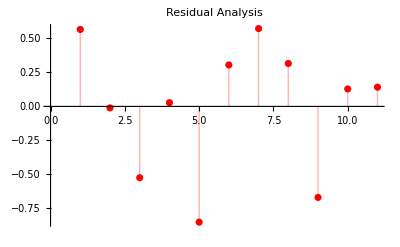

```mathematica
ListPlot[Lm["FitResiduals"],Filling->Axis,PlotStyle->Red,PlotLabel->"Residual Analysis"]
```

(i) ParameterErrors -- standard deviation of the parameter estimate.
(ii) ConfidenceIntervals -- the 95% range where the true physical value likely resides.

```mathematica
Lm[{"BestFitParameters","ParameterErrors","ParameterConfidenceIntervals"}]
```

{{2.8726,9.77867},{0.286933,0.097001},{{2.22351,3.52169},{9.55924,9.9981}}}

Ex-3:

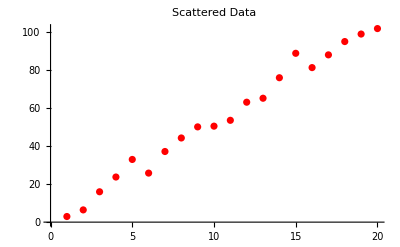

```mathematica
b=2.0;
a=5.0;
SeedRandom[42];
data=Table[{x,a*x+b+RandomVariate[NormalDistribution[0,4]]},{x,1,20}];
ListPlot[data,PlotStyle->Red,PlotLabel->"Scattered  Data"]
```

```mathematica
Lm=LinearModelFit[data,{1,x},x];

slopeValue=Lm["BestFitParameters"][[2]];
slopeError=Lm["ParameterErrors"][[2]];

Print["Estimated Slope: ",slopeValue];
Print["Uncertainty (Error): ",slopeError];
```

Estimated Slope: 5.24526

Uncertainty (Error): 0.15232

```mathematica
constValue=Lm["BestFitParameters"][[1]]
constError=Lm["ParameterErrors"][[1]]
```

-0.0964927

1.82466

```mathematica
tStat=slopeValue/slopeError;
Print["t-Statistic: ",tStat]
```

t-Statistic: 34.4359

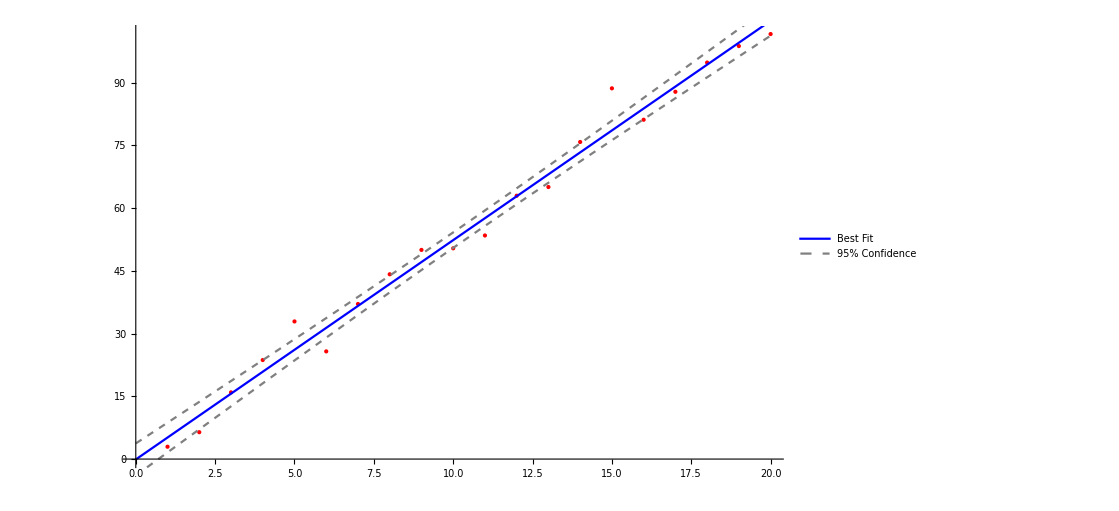

```mathematica
Show[ListPlot[data,PlotStyle->{Red,PointSize[Medium]}],Plot[{Lm[x],Lm["MeanPredictionBands"]},{x,0,20},PlotStyle->{Blue,{Dashed,Gray},{Dashed,Gray}},PlotLegends->{"Best Fit","95% Confidence"}]]
```

"Goodness of Fit" -- the quantitative way to answer the question: "How much should I trust this model?".

χ_ν^2==1/(d.o.f)∑(y_obs-y_fit)^2/σ_error^2   (Reduced Chi-Squared)

```mathematica
b=2.0;
a=5.0;
SeedRandom[42]; (* initialize the pseudo-random number generator *)
data=Table[{x,a*x+b+RandomVariate[NormalDistribution[0,4]]},{x,1,20}];
ListPlot[data,PlotStyle->Red,PlotLabel->"Scattered  Data"]
```

-Graphics-

```mathematica
Lm=LinearModelFit[data,{1,x},x];
```

```mathematica
sigmaError=4.0;
estVar=Lm["EstimatedVariance"];
reducedChiSq=estVar/(sigmaError^2)  (*Calculate Reduced Chi-Squared*)
```

0.964301

Problem-2:
Generate a table of n random numbers using the RandomReal[{-1, 1}] function (note that these numbers are centered at zero). Calculate the Standard Deviation of these n numbers. Repeat this process for n running from 100 to 2000 in steps of 200.

Fit the result to the power-law form:

f(n)==a·n^b

Q. What value is the exponent b closest to ?

```mathematica
ClearAll[a,b,n]
```

```mathematica
data=Table[{n,StandardDeviation[RandomReal[{-1,1},n]]},{n,100,2000,200}];
NLm=NonlinearModelFit[data,a*n^b,{a,b},n];
Print["Best Fit Parameters: ",NLm["BestFitParameters"]];
Print["Parameter Table:"];
NLm["ParameterTable"]
```

Best Fit Parameters: {a→0.523654,b→0.0150457}

Parameter Table:

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.523654 | 0.0225104 | 23.2628 | 1.23873×10^-8
b | 0.0150457 | 0.00640407 | 2.3494 | 0.0467251